#### Scott's version

```mathematica
KnotTheoryPath = "~/projects/KnotTheory/trunk/";
AppendTo[$Path, KnotTheoryPath];
<< KnotTheory`
```

Loading KnotTheory` version of November 19, 2008, 11:39:57.9761.
Read more at http://katlas.org/wiki/KnotTheory.

```mathematica
KnotTheoryDirectory[]
```

/Users/scott/projects/KnotTheory/trunk/KnotTheory

```mathematica
Kh[Knot[3,1],Program->"FastKh"][q,t]
```

1/q^3+1/q+1/(q^9 t^3)+1/(q^5 t^2)

```mathematica
Kh[Knot[3,1],Program->"JavaKh-v1"][q,t]
```

KnotTheory::credits: "The Khovanov homology program JavaKh-v1 was written by Jeremy Green in the summer of 2005 at the University of Toronto."

1/q^3+1/q+1/(q^9 t^3)+1/(q^5 t^2)

```mathematica
Kh[Knot[3,1],Program->"JavaKh-v2"][q,t]
```

KnotTheory::credits: "The Khovanov homology program JavaKh-v2 is an update of Jeremy Green's program JavaKh-v1, written by Scott Morrison in 2008 at Microsoft Station Q."

1/q^3+1/q+1/(q^9 t^3)+1/(q^5 t^2)

```mathematica
With[{K=Knot[3,1],program="JavaKh-v1"},Kh[K,Program->program][q,t]-Kh[K,Program->program,Modulus->2][q,t]]
```

-1/(q^7 t^3)-1/(q^7 t^2)

```mathematica
With[{K=Knot[3,1],program="JavaKh-v2"},Kh[K,Program->program][q,t]-Kh[K,Program->program,Modulus->2][q,t]]
```

-1/(q^7 t^3)-1/(q^7 t^2)

```mathematica
Clear[BenchmarkData]
```

```mathematica
BenchmarkData[tag_String]:={}
```

```mathematica
BenchmarkData[tag_String,n_]:=Cases[BenchmarkData[tag],{_,n,___}]
```

```mathematica
KnotWidth[K_]:=First[BR[K]]
KnotLength[K_]:=Length[BR[K]⟦2⟧]
```

```mathematica
echo[x_]:=(Print[x];x)
```

```mathematica
Off[Unset::norep]
```

```mathematica
Off[Unset::write]
```

```mathematica
Clear[benchmark]
```

```mathematica
benchmark[tag_,invariantFunction_,K_]:=Module[{data},
If[MemberQ[BenchmarkData[tag],{K,___}],Return[]];
data={K,KnotWidth[K],KnotLength[K],Sequence@@(AbsoluteTiming[invariantFunction[BR[K]]]/.Second->1)};
invariantFunction[K]=.;
If[data⟦4⟧>0.5,
Print[data];
AppendTo[BenchmarkData[tag],data];
];
];
```

```mathematica
benchmark[tag_,invariantFunction_,knots_List]:=(benchmark[tag,invariantFunction,#]&/@knots;)
```

```mathematica
benchmark["FastKh",Kh[#,Program->"FastKh","chaff"->Random[]][q,t]&,Take[AllKnots[{11,11}],-10]]
```

KnotTheory::loading: Loading precomputed data in "DTCode4KnotsTo11`".

KnotTheory::credits: "The GaussCode to PD conversion was written by Siddarth Sankaran at the University of Toronto in the summer of 2005."

KnotTheory::credits: "Vogel's algorithm was implemented by Dan Carney in the summer of 2005 at the University of Toronto."

{Knot[11,NonAlternating,176],4,11,10.48699,2/q^3+4/q+1/(q^19 t^8)+2/(q^17 t^7)+1/(q^15 t^7)+4/(q^15 t^6)+2/(q^13 t^6)+5/(q^13 t^5)+4/(q^11 t^5)+5/(q^11 t^4)+5/(q^9 t^4)+6/(q^9 t^3)+5/(q^7 t^3)+4/(q^7 t^2)+6/(q^5 t^2)+3/(q^5 t)+4/(q^3 t)+q t}

{Knot[11,NonAlternating,177],4,11,5.671079,8 q+7 q^3+1/(q^7 t^4)+3/(q^5 t^3)+1/(q^3 t^3)+5/(q^3 t^2)+3/(q t^2)+6/(q t)+(5 q)/t+7 q^3 t+7 q^5 t+6 q^5 t^2+7 q^7 t^2+4 q^7 t^3+6 q^9 t^3+2 q^9 t^4+4 q^11 t^4+2 q^13 t^5}

{Knot[11,NonAlternating,178],4,11,12.45317,5 q+3 q^3+2/(q t)+7 q^3 t+4 q^5 t+8 q^5 t^2+7 q^7 t^2+8 q^7 t^3+8 q^9 t^3+8 q^9 t^4+8 q^11 t^4+5 q^11 t^5+8 q^13 t^5+4 q^13 t^6+5 q^15 t^6+q^15 t^7+4 q^17 t^7+q^19 t^8}

$Aborted

```mathematica
Khv1=Function[{K},Kh[K,Program->"JavaKh-v1","chaff"->Random[]][q,t]];
Khv2=Function[{K},Kh[K,Program->"JavaKh-v2","chaff"->Random[]][q,t]];
```

```mathematica
benchmarkComparision:=Show[Plot[x,{x,0,100}],ListPlot[Cases[Flatten[BenchmarkData["JavaKh-v1"]/.{K_,w_,l_,T1_,Except[$Failed[q,t]]}:>Cases[BenchmarkData["JavaKh-v2"],{K,w,l,T2_,Except[$Failed[q,t]]}:>{T1,T2}],1],{_,_}]],AspectRatio->1,PlotRange->All]
```

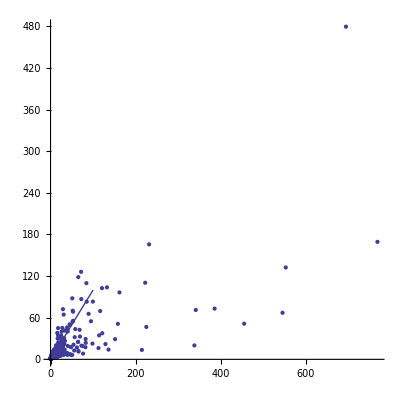

```mathematica
benchmarkComparision
```

```mathematica
SetDirectory[ToFileName[ToFileName[KnotTheoryDirectory[],".."],"testing"]]
```

/Users/scott/projects/KnotTheory/trunk/testing

```mathematica
FileNames["*.m"]
```

{benchmarkdata.m}

```mathematica
<<benchmarkdata.m;
```

```mathematica
Save["benchmarkdata.m",BenchmarkData]
```

{Knot[15,Alternating,23519],4,15,9.375,65/q+61 q+1/(q^15 t^7)+4/(q^13 t^6)+1/(q^11 t^6)+10/(q^11 t^5)+4/(q^9 t^5)+21/(q^9 t^4)+10/(q^7 t^4)+35/(q^7 t^3)+21/(q^5 t^3)+49/(q^5 t^2)+35/(q^3 t^2)+60/(q^3 t)+49/(q t)+62 q t+64 q^3 t+52 q^3 t^2+62 q^5 t^2+38 q^5 t^3+52 q^7 t^3+24 q^7 t^4+38 q^9 t^4+12 q^9 t^5+24 q^11 t^5+5 q^11 t^6+12 q^13 t^6+q^13 t^7+5 q^15 t^7+q^17 t^8}

{Knot[15,Alternating,23519],4,15,3.203125,65/q+61 q+1/(q^15 t^7)+4/(q^13 t^6)+1/(q^11 t^6)+10/(q^11 t^5)+4/(q^9 t^5)+21/(q^9 t^4)+10/(q^7 t^4)+35/(q^7 t^3)+21/(q^5 t^3)+49/(q^5 t^2)+35/(q^3 t^2)+60/(q^3 t)+49/(q t)+62 q t+64 q^3 t+52 q^3 t^2+62 q^5 t^2+38 q^5 t^3+52 q^7 t^3+24 q^7 t^4+38 q^9 t^4+12 q^9 t^5+24 q^11 t^5+5 q^11 t^6+12 q^13 t^6+q^13 t^7+5 q^15 t^7+q^17 t^8}

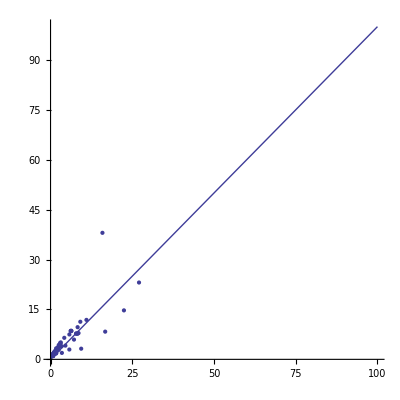

{Knot[15,NonAlternating,134534],6,25,0.921875,4 q^3+2 q^5+q^7+1/(q^3 t^4)+q/t^3+q/t^2+q/t+q^3/t+q^5/t+4 q^5 t+4 q^7 t+6 q^7 t^2+4 q^9 t^2+q^11 t^2+6 q^9 t^3+6 q^11 t^3+6 q^11 t^4+6 q^13 t^4+4 q^13 t^5+6 q^15 t^5+3 q^15 t^6+4 q^17 t^6+q^17 t^7+3 q^19 t^7+q^21 t^8}

{Knot[15,NonAlternating,134534],6,25,1.875,4 q^3+2 q^5+q^7+1/(q^3 t^4)+q/t^3+q/t^2+q/t+q^3/t+q^5/t+4 q^5 t+4 q^7 t+6 q^7 t^2+4 q^9 t^2+q^11 t^2+6 q^9 t^3+6 q^11 t^3+6 q^11 t^4+6 q^13 t^4+4 q^13 t^5+6 q^15 t^5+3 q^15 t^6+4 q^17 t^6+q^17 t^7+3 q^19 t^7+q^21 t^8}

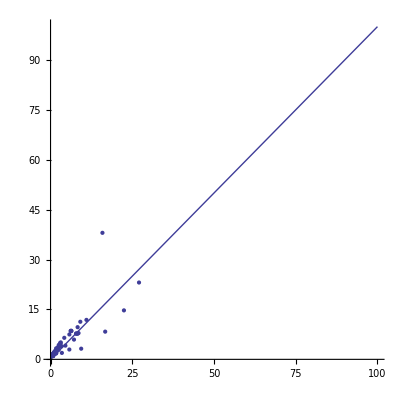

{Knot[15,Alternating,28027],4,15,12.5,69 q+56 q^3+1/(q^11 t^6)+4/(q^9 t^5)+1/(q^7 t^5)+11/(q^7 t^4)+4/(q^5 t^4)+24/(q^5 t^3)+11/(q^3 t^3)+39/(q^3 t^2)+24/(q t^2)+55/(q t)+(39 q)/t+73 q^3 t+68 q^5 t+70 q^5 t^2+73 q^7 t^2+58 q^7 t^3+70 q^9 t^3+43 q^9 t^4+58 q^11 t^4+26 q^11 t^5+43 q^13 t^5+13 q^13 t^6+26 q^15 t^6+5 q^15 t^7+13 q^17 t^7+q^17 t^8+5 q^19 t^8+q^21 t^9}

{Knot[15,Alternating,28027],4,15,3.65625,69 q+56 q^3+1/(q^11 t^6)+4/(q^9 t^5)+1/(q^7 t^5)+11/(q^7 t^4)+4/(q^5 t^4)+24/(q^5 t^3)+11/(q^3 t^3)+39/(q^3 t^2)+24/(q t^2)+55/(q t)+(39 q)/t+73 q^3 t+68 q^5 t+70 q^5 t^2+73 q^7 t^2+58 q^7 t^3+70 q^9 t^3+43 q^9 t^4+58 q^11 t^4+26 q^11 t^5+43 q^13 t^5+13 q^13 t^6+26 q^15 t^6+5 q^15 t^7+13 q^17 t^7+q^17 t^8+5 q^19 t^8+q^21 t^9}

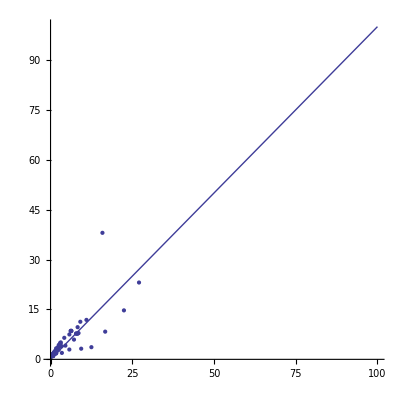

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "C:\scott\projects\KnotTheory\trunk\KnotTheory\JavaKh1"  org.katlas.JavaKh.JavaKh -mod 0 < pd 2> JavaKh.log

There may have been an error log produced by Java:

Exception in thread "main" java.lang.OutOfMemoryError: Java heap space
	at org.katlas.JavaKh.LCCC.<init>(LCCC.java:19)
	at org.katlas.JavaKh.LCCC.compose(LCCC.java:152)
	at org.katlas.JavaKh.Komplex.compose(Komplex.java:1176)
	at org.katlas.JavaKh.Komplex.generateFast(Komplex.java:1092)
	at org.katlas.JavaKh.JavaKh.main(JavaKh.java:43)
Exception in thread "main" java.lang.OutOfMemoryError: Java heap space
	at org.katlas.JavaKh.CannedCobordismImpl.reverseMaps(CannedCobordismImpl.java:163)
	at org.katlas.JavaKh.CannedCobordismImpl.composeWithoutCache(CannedCobordismImpl.java:555)
	at org.katlas.JavaKh.CannedCobordismImpl.compose(CannedCobordismImpl.java:341)
	at org.katlas.JavaKh.CannedCobordismImpl.compose(CannedCobordismImpl.java:1)
	at org.katlas.JavaKh.algebra.implementations.LinearComboMap.compose(LinearComboMap.java:142)
	at org.katlas.JavaKh.LCCCMap.compose(LCCCMap.java:163)
	at org.katlas.JavaKh.LCCCMap.compose(LCCCMap.java:1)
	at org.katlas.JavaKh.algebra.implementations.LinearComboMap.compose(LinearComboMap.java:1)
	at org.katlas.JavaKh.CobMatrix.compose(CobMatrix.java:173)
	at org.katlas.JavaKh.Komplex.blockReductionLemma(Komplex.java:1285)
	at org.katlas.JavaKh.Komplex.blockReductionLemma(Komplex.java:1014)
	at org.katlas.JavaKh.Komplex.reduce(Komplex.java:506)
	at org.katlas.JavaKh.Komplex.generateFast(Komplex.java:1659)
	at org.katlas.JavaKh.JavaKh.main(JavaKh.java:111)

{Knot[15,NonAlternating,128085],8,35,818.328125,$Failed[q,t]}

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "C:\scott\projects\KnotTheory\trunk\KnotTheory\JavaKh2\bin;C:\scott\projects\KnotTheory\trunk\KnotTheory\JavaKh2\jars\commons-cli-1.0.jar;C:\scott\projects\KnotTheory\trunk\KnotTheory\JavaKh2\jars\commons-io-1.2.jar;C:\scott\projects\KnotTheory\trunk\KnotTheory\JavaKh2\jars\commons-logging-1.1.jar;C:\scott\projects\KnotTheory\trunk\KnotTheory\JavaKh2\jars\log4j-1.2.12.jar;C:\scott\projects\KnotTheory\trunk\KnotTheory\JavaKh2\jars\trove-2.0.4.jar"  org.katlas.JavaKh.JavaKh --mod 0 < pd 2> JavaKh.log

There may have been an error log produced by Java:

{Knot[15,NonAlternating,128085],8,35,140.359375,$Failed[q,t]}

-Graphics-

```mathematica
({benchmark["JavaKh-v1",Khv1,#],benchmark["JavaKh-v2",Khv2,#]};Print[benchmarkComparision])&/@RandomSample[AllKnots[{12,15}],100]
```

```mathematica
Map[{#⟦3⟧,#⟦4⟧}&,Split[SortBy[BenchmarkData["FastKh"],#⟦2⟧&],#1⟦2⟧==#2⟦2⟧&],{2}]
```

{{{10,1.359375},{10,1.65625},{10,1.171875}},{{11,1.515625},{11,1.25}},{{12,1.171875},{12,2.078125},{12,1.359375}},{{13,1.34375},{13,1.234375}}}

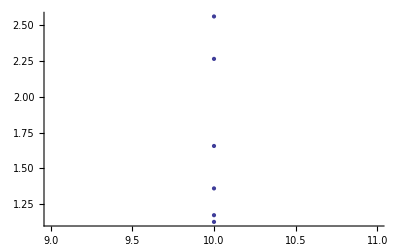
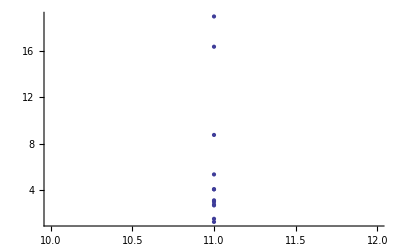
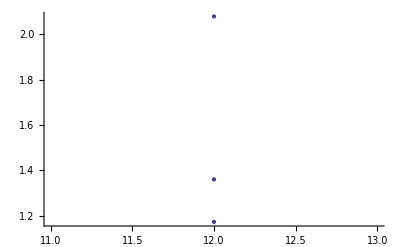
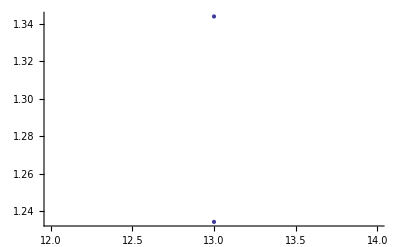

```mathematica
ListPlot/@Map[{#⟦3⟧,#⟦4⟧}&,Split[SortBy[BenchmarkData["FastKh"],#⟦2⟧&],#1⟦2⟧==#2⟦2⟧&],{2}]
```

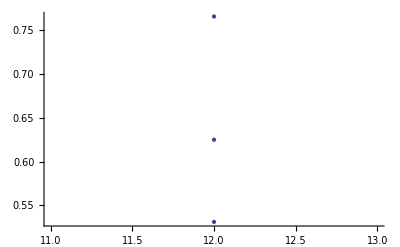
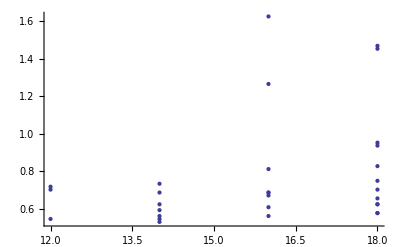
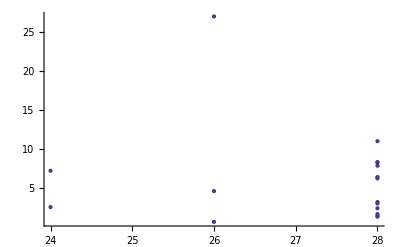
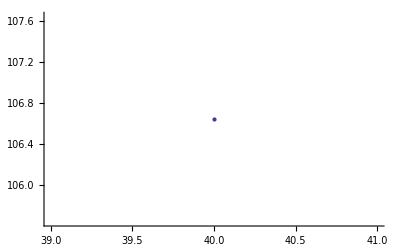

```mathematica
ListPlot/@Map[{#⟦3⟧,#⟦4⟧}&,Split[SortBy[DeleteCases[BenchmarkData["JavaKh-v1"],$Failed[q,t]],#⟦2⟧&],#1⟦2⟧==#2⟦2⟧&],{2}]
```

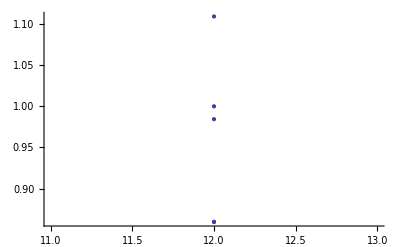
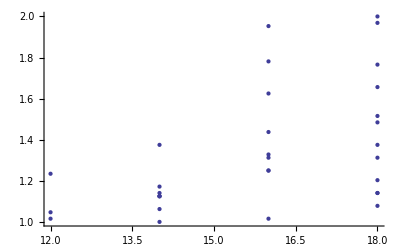
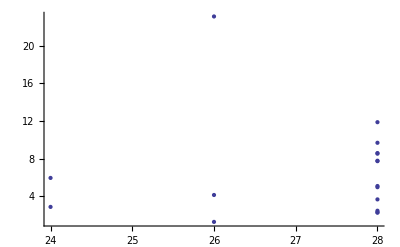
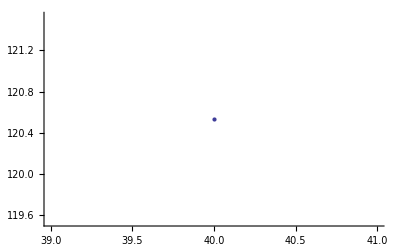

```mathematica
ListPlot/@Map[{#⟦3⟧,#⟦4⟧}&,Split[SortBy[DeleteCases[BenchmarkData["JavaKh-v2"],$Failed[q,t]],#⟦2⟧&],#1⟦2⟧==#2⟦2⟧&],{2}]
```

```mathematica
RandomKnot[n_]:=Module[{k},
k=Random[Integer,{1,NumberOfKnots[n]}];
If[k≤NumberOfKnots[n,Alternating],
Knot[n,Alternating,k],
Knot[n,NonAlternating,k-NumberOfKnots[n,Alternating]]
]
]
```

```mathematica
QuantumKnotInvariantSplit[K,Γ,Irrep[Γ][λ]]
```

```mathematica
QuantumKnotInvariantSplit[#,Subscript[A, 2],Irrep[Subscript[A, 2]][{1,0}]]&[Knot[7,2]]
```

q^2+q^6+q^8+q^16+q^18-q^24-q^26

```mathematica
benchmark["QuantumA2",QuantumKnotInvariantSplit[#,Subscript[A, 2],Irrep[Subscript[A, 2]][{1,0}]]&,Table[TorusKnot[n,5],{n,5,100}]]
```

14 dim: 30 mem: 12381448 time: 1454.79

12 dim: 30 mem: 12382008 time: 1454.89

8 dim: 30 mem: 12382336 time: 1455.

17 dim: 20 mem: 12382664 time: 1455.13

11 dim: 20 mem: 12382928 time: 1455.19

6 dim: 20 mem: 12383192 time: 1455.24

Unset::write: Tag Function in (QuantumKnotInvariantSplit[#1, A_2, Irrep[A_2][{1, 0}]] &)[TorusKnot[5, 5]] is Protected. More…

{TorusKnot[5,5],5,20,2.322575}

Unset::write: Tag Function in (QuantumKnotInvariantSplit[#1, A_2, Irrep[A_2][{1, 0}]] &)[TorusKnot[6, 5]] is Protected. More…

14 dim: 30 mem: 12404776 time: 1455.53

12 dim: 30 mem: 12405096 time: 1456.61

8 dim: 30 mem: 12405424 time: 1457.82

17 dim: 20 mem: 12405752 time: 1458.82

11 dim: 20 mem: 12406016 time: 1459.08

6 dim: 20 mem: 12406280 time: 1459.39

Unset::write: Tag Function in (QuantumKnotInvariantSplit[#1, A_2, Irrep[A_2][{1, 0}]] &)[TorusKnot[10, 5]] is Protected. More…

General::stop: Further output of Unset :: "write" will be suppressed during this calculation. More…

{TorusKnot[10,5],5,40,16.458248}

14 dim: 30 mem: 12436896 time: 1460.13

12 dim: 30 mem: 12437080 time: 1464.24

8 dim: 30 mem: 12437240 time: 1471.16

17 dim: 20 mem: 12437400 time: 1477.49

11 dim: 20 mem: 12437560 time: 1479.01

6 dim: 20 mem: 12437720 time: 1480.51

{TorusKnot[14,5],5,56,42.8074636}

14 dim: 30 mem: 12448536 time: 1482.98

12 dim: 30 mem: 12449000 time: 1499.16

8 dim: 30 mem: 12449328 time: 1516.37

17 dim: 20 mem: 12449656 time: 1533.83

11 dim: 20 mem: 12449920 time: 1537.64

6 dim: 20 mem: 12450184 time: 1541.42

{TorusKnot[15,5],5,60,74.2222954}

14 dim: 30 mem: 12493152 time: 1548.26

12 dim: 30 mem: 12493448 time: 1555.01

8 dim: 30 mem: 12493608 time: 1567.04

17 dim: 20 mem: 12493768 time: 1578.95

11 dim: 20 mem: 12493928 time: 1581.68

6 dim: 20 mem: 12494088 time: 1584.38

{TorusKnot[16,5],5,64,41.1356099}

14 dim: 30 mem: 12506752 time: 1587.99

12 dim: 30 mem: 12507048 time: 1623.82

8 dim: 30 mem: 12507208 time: 1662.14

17 dim: 20 mem: 12507368 time: 1700.02

11 dim: 20 mem: 12507528 time: 1707.78

6 dim: 20 mem: 12507688 time: 1715.47

{TorusKnot[17,5],5,68,154.551362}

14 dim: 30 mem: 12517520 time: 1728.47

$Aborted

```mathematica
benchmark["Jones",Jones,TorusKnots[100]]
```

{TorusKnot[8,7],7,48,47.718616}

{TorusKnot[12,5],5,48,5.1273728}

{TorusKnot[25,3],3,50,0.6208928}

{TorusKnot[17,4],4,51,1.802592}

{TorusKnot[13,5],5,52,6.8498496}

{TorusKnot[26,3],3,52,0.600864}

{TorusKnot[9,7],7,54,67.5371136}

{TorusKnot[11,6],6,55,23.303509}

$Aborted

```mathematica
benchmark["HOMFLYPT",HOMFLYPT,TorusKnots[100]]
```

KnotTheory::credits: "The HOMFLYPT program was written by Scott Morrison."

{TorusKnot[15,2],2,15,0.9113104}

{TorusKnot[8,3],3,16,1.071541}

{TorusKnot[17,2],2,17,2.473557}

{TorusKnot[19,2],2,19,6.8698784}

{TorusKnot[10,3],3,20,14.02016}

{TorusKnot[7,4],4,21,27.840032}

{TorusKnot[21,2],2,21,19.127504}

{TorusKnot[11,3],3,22,22.993062}

{TorusKnot[23,2],2,23,53.526968}

{TorusKnot[6,5],5,24,109.587579}

$Aborted

```mathematica
benchmark["A2Invariant",A2Invariant,TorusKnots[100]]
```

{TorusKnot[7,3],3,14,1.321901}

{TorusKnot[5,4],4,15,36.4123584}

{TorusKnot[8,3],3,16,1.872693}

{TorusKnot[10,3],3,20,3.7453856}

{TorusKnot[7,4],4,21,241.907846}

{TorusKnot[11,3],3,22,5.3476896}

$Aborted

```mathematica
benchmark["A2Invariant",A2Invariant,Table[TorusKnot[n,4],{n,6,100}]]
```

{TorusKnot[6,4],4,18,105.221301}

$Aborted

```mathematica
BenchmarkData["A2Invariant"]
```

{{TorusKnot[7,3],3,14,1.321901},{TorusKnot[5,4],4,15,36.4123584},{TorusKnot[8,3],3,16,1.872693},{TorusKnot[10,3],3,20,3.7453856},{TorusKnot[7,4],4,21,241.907846},{TorusKnot[11,3],3,22,5.3476896}}

```mathematica
Sort[{#⟦2⟧,#⟦3⟧,(#⟦4⟧)/(#⟦3⟧)^2}&/@BenchmarkData["A2Invariant"]]
```

{{3,14,0.006744392},{3,16,0.007315206},{3,20,0.009363464},{3,22,0.011048945},{3,26,0.013747579},{3,28,0.014753357},{3,30,0.015566828},{3,32,0.015989789},{3,34,0.016892803},{4,15,0.161832704},{4,21,0.548543869}}

```mathematica
Sort[{#⟦2⟧,#⟦3⟧,(#⟦4⟧)/(#⟦3⟧)^3}&/@BenchmarkData["A2Invariant"]]
```

{{3,14,0.0004817423},{3,16,0.0004572004},{3,20,0.0004681732},{3,22,0.00050222479},{3,26,0.00052875303},{3,28,0.00052690561},{3,30,0.00051889428},{3,32,0.00049968091},{3,34,0.00049684714},{4,15,0.0107888469},{4,18,0.0180420612},{4,21,0.0261211366}}

```mathematica
Sort[{#⟦2⟧,#⟦3⟧,(#⟦4⟧)/(#⟦3⟧)^5.5}&/@BenchmarkData["A2Invariant"]]
```

{{3,14,6.56893×10^-7},{3,16,4.46485×10^-7},{3,20,2.61717×10^-7},{3,22,2.21229×10^-7},{3,26,1.53398×10^-7},{3,28,1.2701×10^-7},{3,30,1.05263×10^-7},{3,32,8.62617×10^-8},{3,34,7.37098×10^-8},{4,15,0.0000123807},{4,18,0.0000131252},{4,21,0.0000129254}}

```mathematica
Sort[{#⟦2⟧,#⟦3⟧,(#⟦4⟧)/(#⟦3⟧)^3}&/@BenchmarkData["QuantumA2",3]]
```

{{3,44,6.701033×10^-6},{3,46,6.584631×10^-6},{3,50,6.729677×10^-6},{3,52,6.766102×10^-6}}

```mathematica
Sort[{#⟦2⟧,#⟦3⟧,(#⟦4⟧)/(#⟦3⟧)^4.5}&/@BenchmarkData["QuantumA2",4]]
```

{{4,27,1.99458×10^-7},{4,33,1.73458×10^-7},{4,39,1.72597×10^-7},{4,45,1.68922×10^-7},{4,51,1.74323×10^-7}}

```mathematica
Sort[{#⟦2⟧,#⟦3⟧,(#⟦4⟧)/(#⟦3⟧)^9.5}&/@BenchmarkData["HOMFLYPT",2]]
```

{{2,15,6.12068×10^-12},{2,17,5.05891×10^-12},{2,19,4.88416×10^-12},{2,21,5.25503×10^-12},{2,23,6.19667×10^-12}}

```mathematica
Sort[{#⟦2⟧,#⟦3⟧,(#⟦4⟧)/(1.67)^(#⟦3⟧)}&/@BenchmarkData["HOMFLYPT",2]]
```

{{2,15,0.000415833},{2,17,0.000404708},{2,19,0.000403029},{2,21,0.000402358},{2,23,0.000403733}}

```mathematica
{EstimatedVariance,BestFitParameters}/.NonlinearRegress[BenchmarkData["Jones",5]⟦All,{2,3}⟧,α l^n,{l},{α,n},RegressionReport->{BestFitParameters,EstimatedVariance}]
```

{133.486,{α→9.27742,n→0.871394}}

```mathematica
Sort[{#⟦2⟧,#⟦3⟧,(#⟦4⟧)/(#⟦3⟧)^2.6}&/@BenchmarkData["Jones",5]]
```

{{5,24,0.000198869},{5,28,0.000193746},{5,32,0.000209041},{5,36,0.000197098},{5,44,0.000220596},{5,48,0.000218106},{5,52,0.000236631}}

```mathematica
model[power]:={α l^n ,{l},{α,n}}
```

```mathematica
<<Statistics`NonlinearFit`
```

```mathematica
tryModel[tag_,width_,model_List]:={EstimatedVariance,BestFitParameters}/.NonlinearRegress[BenchmarkData[tag,width]⟦All,{3,4}⟧,Sequence@@model,RegressionReport->{BestFitParameters,EstimatedVariance}]
```

```mathematica
tryModel["A2Invariant",3,model[power]]
```

{0.10467,{α→0.000624527,n→2.938792}}

```mathematica
<<Graphics`Graphics3D`
```

```mathematica
graphModel[tag_,width_,model_List,options___]:=Module[{f=model⟦1⟧/.tryModel[tag,width,model]⟦2⟧,modulePlot,dataPlot},
modelPlot=Plot[f,Evaluate[{l,Min[#],Max[#]}&[BenchmarkData[tag,width]⟦All,{3,4}⟧],PlotRange->All,DisplayFunction->Identity]];
dataPlot=ListPlot[BenchmarkData[tag,width]⟦All,{3,4}⟧,PlotJoined->True,DisplayFunction->Identity];
Show[modelPlot,dataPlot,options,DisplayFunction->$DisplayFunction]
]
```

```mathematica
BenchmarkData["A2Invariant",3]
```

{{TorusKnot[7,3],3,14,1.321901},{TorusKnot[8,3],3,16,1.872693},{TorusKnot[10,3],3,20,3.7453856},{TorusKnot[11,3],3,22,5.3476896},{TorusKnot[13,3],3,26,9.2933632},{TorusKnot[14,3],3,28,11.566632},{TorusKnot[15,3],3,30,14.010146},{TorusKnot[16,3],3,32,16.373544},{TorusKnot[17,3],3,34,19.52808}}

```mathematica
tryModel["A2Invariant",3,model[power]]
```

{0.10467,{α→0.000624527,n→2.938792}}

```mathematica
graphModel["A2Invariant",3,model[power]]
```

⁃Graphics⁃

```mathematica
BenchmarkData["A2Invariant",4]
```

{{TorusKnot[5,4],4,15,36.4123584},{TorusKnot[7,4],4,21,241.907846},{TorusKnot[6,4],4,18,105.221301}}

```mathematica
tryModel["A2Invariant",4,model[power]]
```

{4.96447,{α→0.0000131542018,n→5.49467113}}

```mathematica
graphModel["A2Invariant",4,model[power]]
```

⁃Graphics⁃

```mathematica
BenchmarkData["QuantumA2",4]
```

{{TorusKnot[9,4],4,27,0.550792},{TorusKnot[11,4],4,33,1.181699},{TorusKnot[13,4],4,39,2.493586},{TorusKnot[15,4],4,45,4.6466816},{TorusKnot[17,4],4,51,8.4221104},{TorusKnot[18,4],4,54,78.7162808},{TorusKnot[6,4],4,18,3.5834726},{TorusKnot[8,4],4,24,4.4242874},{TorusKnot[10,4],4,30,4.6244814},{TorusKnot[12,4],4,36,3.5634532},{TorusKnot[14,4],4,42,5.5754029},{TorusKnot[16,4],4,48,4.5143747},{TorusKnot[19,4],4,57,17.627082},{TorusKnot[20,4],4,60,10.920583},{TorusKnot[21,4],4,63,24.143396},{TorusKnot[22,4],4,66,14.584133}}

```mathematica
tryModel["QuantumA2",4,model[power]]
```

{308.869,{α→0.003222899,n→2.153418}}

```mathematica
graphModel["QuantumA2",4,model[power]]
```

⁃Graphics⁃

```mathematica
Sort[BenchmarkData["QuantumA2",5]]
```

{{TorusKnot[5,5],5,20,2.322575},{TorusKnot[7,5],5,28,1.101584},{TorusKnot[8,5],5,32,1.181699},{TorusKnot[9,5],5,36,4.0358032},{TorusKnot[10,5],5,40,16.458248},{TorusKnot[11,5],5,44,11.486517},{TorusKnot[12,5],5,48,8.4521536},{TorusKnot[13,5],5,52,28.711285},{TorusKnot[14,5],5,56,42.8074636},{TorusKnot[15,5],5,60,74.2222954},{TorusKnot[16,5],5,64,41.1356099},{TorusKnot[17,5],5,68,154.551362}}

```mathematica
tryModel["QuantumA2",5,model[power]]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations. More…

{329.599,{α→6.730601×10^-11,n→6.708082}}

```mathematica
graphModel["QuantumA2",5,model[power]]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations. More…

⁃Graphics⁃